# Solve sparse matrix equations

## Solve for the steady state

## Function for solving for one instance of parameters

```mathematica
sparseindex[l_Integer,m_Integer]:=m+(l/2)^2-(-1+m) KroneckerDelta[0,m]/;EvenQ[l]&&EvenQ[m];
```

```mathematica
solveAugmented[numλ_,numinvPe_,numStEff_]:=Module[{parameters,matrix,b,x},
PrintTemporary[StringJoin["λ: ", ToString[numλ//N], ", invPe: ", ToString[numinvPe//N], " and stEff: ", ToString[numStEff//N]]];
parameters = {λ->numλ,Λ->(numλ^2-1)/(numλ^2+1),invPe->numinvPe,stEff->numStEff};
matrix=SparseArray[(ArrayRules[sparseAugmented]/.parameters)/.{(pos_->val_):>(pos->N[val])},Dimensions[sparseAugmented]];
b=N[augmentedB/.parameters];
x=Prepend[LinearSolve[matrix,b],1/(2Sqrt[Pi])//N](*prepend c00*)
];
```

showConvegence plots the magnitude of coefficients, they should be small for high indices.

```mathematica
showConvergence[params___]:=Module[{x},
x=Abs[solveAugmented[params]];
{ListLogPlot[x,PlotRange->Full],ListPlot[x,PlotRange->Full],ListLogLogPlot[x,PlotRange->Full]}
];
```

## Load augmented matrix from file

{40400,40400}

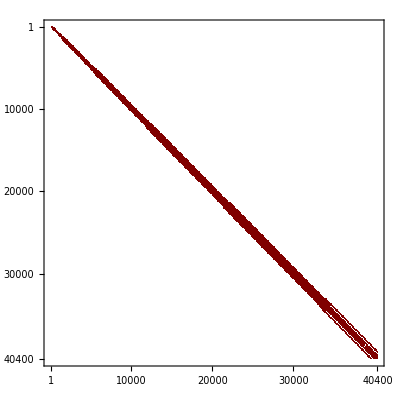

```mathematica
maxl = 400;
Get[ToString[StringForm["augmentedMatrix_lmax``.mx",maxl]]]
Dimensions[sparseAugmented]
MatrixPlot[sparseAugmented]
```

## Check convergence for some particular values of the parameters

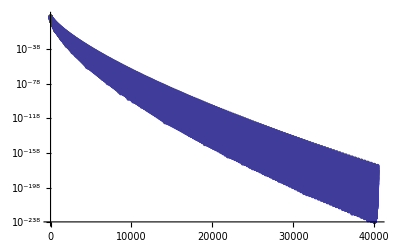
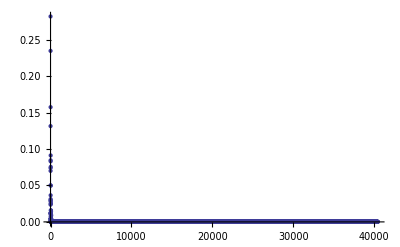
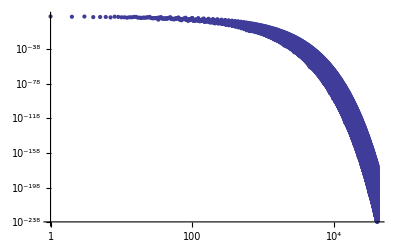

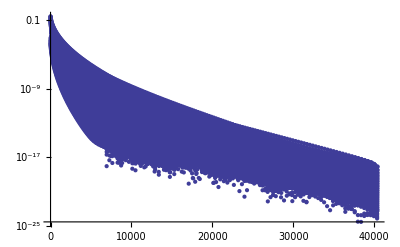
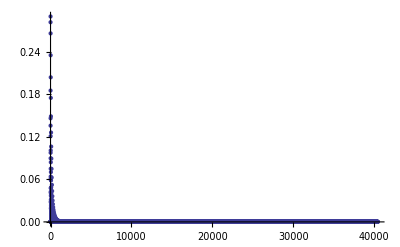
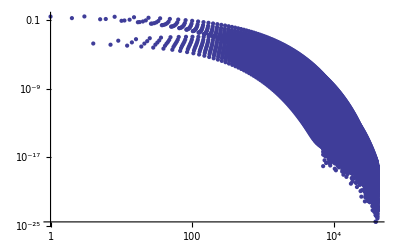

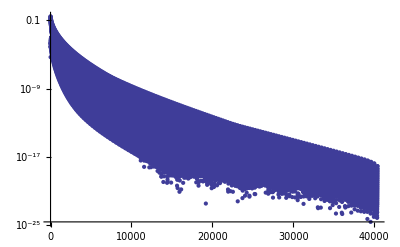
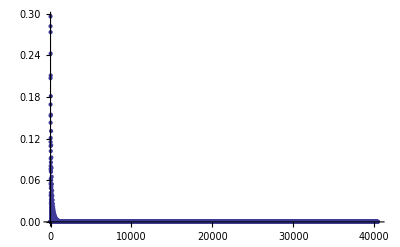

```mathematica
showConvergence[10,1/100,0.0]
showConvergence[10,1/100000,0.0]
showConvergence[10,1/100000,1/100]
```

## Extract angular averages etc from the coefficients

```mathematica
c00idx = sparseindex[0,0];
c20idx = sparseindex[2,0];
c22imidx = sparseindex[2,2]+1;
c40idx = sparseindex[4,0];
c44idx = sparseindex[4,4];
```

```mathematica
sinSqrTheta[x_]:=1-(2/3 √π x[[c00idx]]+4/3 √(π/5)x[[c20idx]]);
```

## For example, reproduce a row from table 6c of Brenner 1974:

```mathematica
ParallelTable[solveAugmented[l,1/10,0.0]//sinSqrTheta,{l,{1,2,3,4,5,7,10,16,25,50}}]//MatrixForm
```

(0.666667
0.682753
0.696383
0.703393
0.707167
0.710763
0.7128
0.714035
0.714511
0.714761)

## Reproduce figs for paper (export data)

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)]; (*helper*)
```

## Figure 1 (function of Pe, various St)

```mathematica
pes=logspace[0,7,30]
sts=Prepend[logspace[-4,-1,4],0.0]
```

```mathematica
fig1prolate5=Table[
ParallelTable[solveAugmented[5,1/pe,st]//sinSqrTheta,{pe,pes}]
,{st,sts}];
fig1oblate5=Table[
ParallelTable[solveAugmented[1/5,1/pe,st]//sinSqrTheta,{pe,pes}]
,{st,sts}];
```

```mathematica
Export["fig1.h5",{pes,sts,fig1prolate5,fig1oblate5},{"Datasets",{"pes","sts","prolate5","oblate5"}}]
```

## Figure 2 (function of PeSt, various k=St/Pe)

```mathematica
pests=logspace[-6,3,20];
ks=logspace[-9,-3,7];
```

```mathematica
fig2prolate5=Table[
ParallelTable[solveAugmented[5,1/Sqrt[pest/k],Sqrt[k pest]]//sinSqrTheta,{pest,pests}]
,{k,ks}];
fig2oblate5=Table[
ParallelTable[solveAugmented[1/5,1/Sqrt[pest/k],Sqrt[k pest]]//sinSqrTheta,{pest,pests}]
,{k,ks}];
```

```mathematica
Export["fig2.h5",{pests,ks,fig2prolate5,fig2oblate5},{"Datasets",{"pests","ks","prolate5","oblate5"}}]
```

## turitsyn

```mathematica
pes=logspace[0,7,10]
```

{1.,5.99484,35.9381,215.443,1291.55,7742.64,46415.9,278256.,1.6681×10^6,1.×10^7}

```mathematica
fig3prolate5=ParallelTable[solveAugmented[50,1/pe,0]//sinSqrTheta,{pe,pes}];
fig3oblate5=ParallelTable[solveAugmented[1/50,1/pe,0]//sinSqrTheta,{pe,pes}];
```

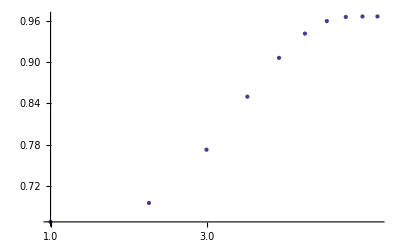

-Graphics-

```mathematica
ListLogLinearPlot[fig3prolate5]
ListLogLinearPlot[fig3oblate5]
```